# Mathematica Final Project Proposal

Logan Houchens and Brian Carlson

## General Idea

Our idea is to analyze and make predictions from social media data. We hope to analyze information that we pull from public posts to make predictions about the gender of the person posting, region/state/city of the United States that they are from, and the periodicity of posts made.

```mathematica
CreateDocument[{TextCell["General Word Usage Difference Per Gender","Title"],TextCell[w,"Text"]},WindowFrame->"Palette",WindowTitle->"Analysis Of Paper",StyleDefinitions->"Creative/PastelColor.nb"];
```

```mathematica
w=Row[{Panel[Column[{-Graphics-,-Graphics-}],TextCell[Style["An example graph with fake data. Each prediction from previous data would be displayed with graphs similar to these to back up predictions our program makes.",FontFamily->"Times"],"Text"],{Bottom}],Column[{PopupMenu["Facebook",{"Facebook","Twitter","LinkedIn","GooglePlus"}],}]}];
```

```mathematica
TreePlot[{"Title Screen"-> "Tool Menu","Tool Menu"-> "Explanation Screen","Tool Menu"-> "Prediction","Explanation Screen"-> "Tool Menu","Tool Menu"-> "Compare Screen","Compare Screen"-> "Tool Menu","Load Menu"-> "Tool Menu","Tool Menu"-> "Load Menu","Compare Screen"->"Result Screen", "Result Screen"-> "Save Menu","Prediction"-> "Result Screen","Result Screen"-> "Save Menu","Prediction"-> "Tool Menu"},Center,VertexLabeling->True]
```

## Finished Appearance

### Screen View

We plan to have our project displayed in a graphical user interface with drop-down boxes, menu screens, and easy-to-use analytical tools.

1.) The finished project, Verbum Usus (Meaning “Word Usage” in Latin) (1.) will open in a new window, bringing up the title screen (See Diagram I). On the title screen, the user has the option to select Facebook or Twitter (hopefully adding Instagram, LinkedIn, and GooglePlus) from the drop down box (2.) to analyze using the tools provided on the next screen. The “Begin” button (3.) will take the user to the next screen (II).

2.) The Tool Menu (Diagram II) will have a drop down box (1.) for choosing past trends to compare, including, but not limited to: word usage for each gender, periodicity of word usage, and word usage in certain locations. When “Compare” is clicked, the user will be taken to the “Compare” window (III). If the user wishes to know the methods we used to extract data and the way we predicted things, he/she can click on the “Explanations and Methods” button (2.) to go to the “Explanations and Methods”. The user can click “Predict” after selecting an option from the dropdown box (3.) to go to the prediction screen to select parameters for determining the option they selected. Also included in this display is a graph (4.) randomly chosen from a list of plots showing some information pulled from the selected social network.

3.) The Compare window (III) will have drop down boxes similar to (1.) and (2.) for specifying what you’d like to compare. Also included will be a filter for selecting a range of dates to pull posts from (3.) and the number of public users to randomly select (4.). When finished, clicking the “Compute” button will take the user to the “Results” screen (IV).

4.) The Results screen (IV) will have the corresponding graphs to appropriately display the data we processed (1.). Each type of comparision will have the most important information shown relevant to that comparision (2.). The resulting statistical information can be accessed by clicking on the button wit the same name. (3.) The results can be saved by clicking the “Save” button. (4.)

#### Click Flow

This is a graph of the screen changes that will take place within our program.

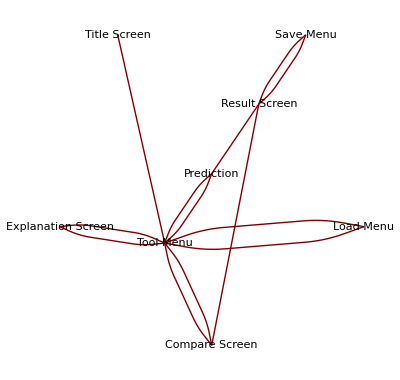

## Goals

### Increments

#### 1. (Week 0-1)

1.) Get authorization from the Institutional Review Board to study human beings.
2.) Write functions to anonymize Facebook/Twitter user data.
3.) Write functions to access individual parts of data.

#### Hurdles

authorization by irb
anonymizing data
filtering out words

### Long Term

1.)

### goals

collect comments, posts on males and females at different locations, form perdictions from an analysis of the data, word analysis, geographical word usage, emoticon usage and charts to describe the data.

maybe include likes later on

maybe include time dependence